```mathematica
SetOptions[SelectedNotebook[],NotebookAutoSave->True](*save notebook after each evaluation*)
```

## Hydrogen Wave Functions

```mathematica
Y[l_,m_,θ_,ϕ_]:=SphericalHarmonicY[l,m,θ,ϕ];
R[n_,l_,r_]:=√((2/n)^3((n-l-1)!)/(2n(n+l)!))((2r)/n)^l LaguerreL[n-l-1,2l+1,2r/n]Exp[-r/n];
PSI[n_,l_,m_,r_,θ_,ϕ_]:=R[n,l,r]*Y[l,m,θ,ϕ];
```

#### Examples: n = 2 states

```mathematica
nn=2;
lmax=nn-1;
Grid[Prepend[Table[Prepend[Table[If[Abs[m]<=l,PSI[nn,l,m,r,θ,ϕ],""],{m,-lmax,lmax}],Row[{"l = ",l}]],{l,0,lmax}],Join[{""},Table[Row[{"m = ",m}],{m,-lmax,lmax}]]],Frame->All]
```

| m = -1 | m = 0 | m = 1
l = 0 |  | (ⅇ^(-r/2) (2-r))/(4 √(2 π)) | 
l = 1 | (ⅇ^(-r/2-ⅈ ϕ) r Sin[θ])/(8 √π) | (ⅇ^(-r/2) r Cos[θ])/(4 √(2 π)) | -(ⅇ^(-r/2+ⅈ ϕ) r Sin[θ])/(8 √π)

#### Examples: n = 3 states

```mathematica
nn=3;
lmax=nn-1;
Grid[Prepend[Table[Prepend[Table[If[Abs[m]<=l,PSI[nn,l,m,r,θ,ϕ],""],{m,-lmax,lmax}],Row[{"l = ",l}]],{l,0,lmax}],Join[{""},Table[Row[{"m = ",m}],{m,-lmax,lmax}]]],Frame->All]
```

| m = -2 | m = -1 | m = 0 | m = 1 | m = 2
l = 0 |  |  | (ⅇ^(-r/3) (27-18 r+2 r^2))/(81 √(3 π)) |  | 
l = 1 |  | (ⅇ^(-r/3-ⅈ ϕ) (4-(2 r)/3) r Sin[θ])/(54 √π) | (ⅇ^(-r/3) (4-(2 r)/3) r Cos[θ])/(27 √(2 π)) | -(ⅇ^(-r/3+ⅈ ϕ) (4-(2 r)/3) r Sin[θ])/(54 √π) | 
l = 2 | (ⅇ^(-r/3-2 ⅈ ϕ) r^2 Sin[θ]^2)/(162 √π) | (ⅇ^(-r/3-ⅈ ϕ) r^2 Cos[θ] Sin[θ])/(81 √π) | (ⅇ^(-r/3) r^2 (-1+3 Cos[θ]^2))/(81 √(6 π)) | -(ⅇ^(-r/3+ⅈ ϕ) r^2 Cos[θ] Sin[θ])/(81 √π) | (ⅇ^(-r/3+2 ⅈ ϕ) r^2 Sin[θ]^2)/(162 √π)

#### Testing normalization

```mathematica
nn=3;ll=2;mm=2;
NIntegrate[
r^2Sin[θ]*
Abs[PSI[nn,ll,mm,r,θ,ϕ]]^2,
{r,0,∞},{θ,0,π},{ϕ,0,2π}
]
```

1.

## Example 8.1, McIntyre

Find the probability that the electron in the ground state of hydrogen is measured to be within one Bohr radius of the nucleus and calculate the expectation value of the radial position r.

```mathematica
nn=1;ll=0;mm=0;
NIntegrate[
r^2Sin[θ]*
Abs[PSI[nn,ll,mm,r,θ,ϕ]]^2,
{r,0,1},{θ,0,π},{ϕ,0,2π}
]
```

0.323324

```mathematica
nn=1;ll=0;mm=0;
NIntegrate[
r^2Sin[θ]*
r*Abs[PSI[nn,ll,mm,r,θ,ϕ]]^2,
{r,0,∞},{θ,0,π},{ϕ,0,2π}
]
```

1.5

## Example 8.2, McIntyre

Find the time evolution of an equal superposition of the 1s ground state and the 2p0 (m=0) excited state. This models an oscillating electric dipole moment.

```mathematica
psi82[r_,θ_,ϕ_,t_]:=1/(√2)PSI[1,0,0,r,θ,ϕ]Exp[(-I t)/1^2]+1/(√2)PSI[2,1,0,r,θ,ϕ]Exp[(-I t)/2^2];
```

#### Convert to Cartesian coordinates to create density plot in x-z plane

```mathematica
psiXZ[x_,z_,t_]:=Module[{r,θ,φ},r=Sqrt[x^2+z^2];
θ=If[r==0,0,ArcCos[z/r]];
φ=If[x>=0,0,Pi];
psi82[r,θ,φ,t]];
```

#### Plot Abs[psi]^2 with rescaling for good contrast

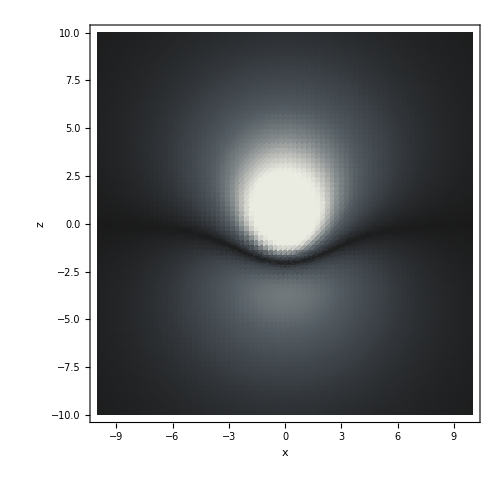

```mathematica
vmax=0.005;   (*tune this*)
gamma=0.4;    (* <1 increases contrast*)

DensityPlot[With[{val=Abs[psiXZ[x,z,0]]^2},(Rescale[Log[1+val],{0,Log[1+vmax]}])^gamma],{x,-10,10},{z,-10,10},ColorFunction->"GrayTones",ColorFunctionScaling->False,PlotPoints->80,PlotRange->{0,5},FrameLabel->{"x","z"},BaseStyle->18,ImageSize->500]
```

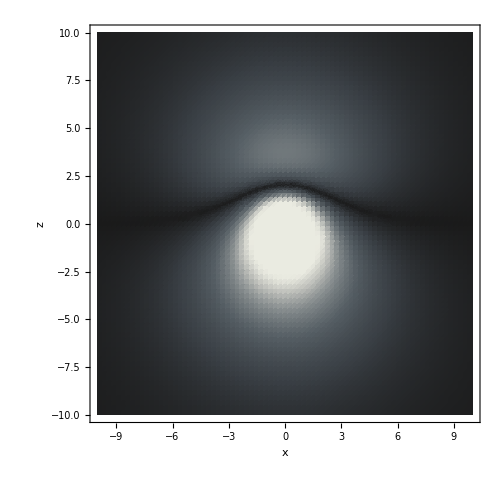

```mathematica
DensityPlot[With[{val=Abs[psiXZ[x,z,4Pi/3]]^2},(Rescale[Log[1+val],{0,Log[1+vmax]}])^gamma],{x,-10,10},{z,-10,10},ColorFunction->"GrayTones",ColorFunctionScaling->False,PlotPoints->80,PlotRange->{0,5},FrameLabel->{"x","z"},BaseStyle->18,ImageSize->500]
```

#### Expectation value of (x, y, z) = (r sin(θ) cos(ϕ), r sin(θ) sin(ϕ), r cos(θ))

```mathematica
(* <x> *)
Assuming[
{Element[t,Reals]},
Integrate[
r^2Sin[θ]*
r*Sin[θ]*Cos[ϕ]Abs[psi82[r,θ,φ,t]]^2,
{r,0,∞},{θ,0,π},{ϕ,0,2π}
]
]
```

0

```mathematica
(* <y> *)
Assuming[
{Element[t,Reals]},
Integrate[
r^2Sin[θ]*
r*Sin[θ]*Sin[ϕ]Abs[psi82[r,θ,φ,t]]^2,
{r,0,∞},{θ,0,π},{ϕ,0,2π}
]
]
```

0

```mathematica
(* <z> *)
Assuming[
{Element[t,Reals]},
Integrate[
r^2Sin[θ]*
r*Cos[θ]*Abs[psi82[r,θ,φ,t]]^2,
{r,0,∞},{θ,0,π},{ϕ,0,2π}
]
]
```

128/243 √2 Cos[(3 t)/4]

The expectation value of the dipole moment is time dependent and oscillates with Bohr frequency.

## Example 8.3, McIntyre

Find the time evolution of an equal superposition of the 2s excited state and the 2p0 (m=0) excited state. This models a static electric dipole moment.

```mathematica
psi83[r_,θ_,ϕ_,t_]:=1/(√2)PSI[2,0,0,r,θ,ϕ]Exp[(-I t)/2^2]+1/(√2)PSI[2,1,0,r,θ,ϕ]Exp[(-I t)/2^2];
```

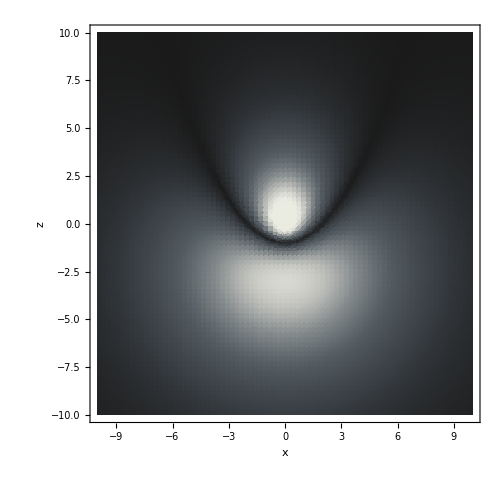

```mathematica
psi83XZ[x_,z_,t_]:=Module[{r,θ,φ},r=Sqrt[x^2+z^2];
θ=If[r==0,0,ArcCos[z/r]];
φ=If[x>=0,0,Pi];
psi83[r,θ,φ,t]];

vmax=0.005;   (*tune this*)
gamma=0.4;    (* <1 increases contrast*)

DensityPlot[With[{val=Abs[psi83XZ[x,z,0]]^2},(Rescale[Log[1+val],{0,Log[1+vmax]}])^gamma],{x,-10,10},{z,-10,10},ColorFunction->"GrayTones",ColorFunctionScaling->False,PlotPoints->80,PlotRange->{0,5},FrameLabel->{"x","z"},BaseStyle->18,ImageSize->500]
```

#### Expectation value of (x, y, z) = (r sin(θ) cos(ϕ), r sin(θ) sin(ϕ), r cos(θ))

```mathematica
(* <x> *)
Assuming[
{Element[t,Reals]},
Integrate[
r^2Sin[θ]*
r*Sin[θ]*Cos[ϕ]Abs[psi83[r,θ,φ,t]]^2,
{r,0,∞},{θ,0,π},{ϕ,0,2π}
]
]
```

0

```mathematica
(* <y> *)
Assuming[
{Element[t,Reals]},
Integrate[
r^2Sin[θ]*
r*Sin[θ]*Sin[ϕ]Abs[psi83[r,θ,φ,t]]^2,
{r,0,∞},{θ,0,π},{ϕ,0,2π}
]
]
```

0

```mathematica
(* <z> *)
Assuming[
{Element[t,Reals]},
Integrate[
r^2Sin[θ]*
r*Cos[θ]*Abs[psi83[r,θ,φ,t]]^2,
{r,0,∞},{θ,0,π},{ϕ,0,2π}
]
]
```

-3

Expectation value of the dipole moment is time independent.